```mathematica
SetDirectory["~/sync/data/multissdb/Top8000-best_hom70_pdb_chain"];
data = Map[Association[Import[#,"JSON"]]&,FileNames[]];
all3= Merge[Map[Counts[#["All3"]]&,data],Total];
dssp3 = Merge[Map[Counts[#["Dssp3"]]&,data],Total];
stride3 = Merge[Map[Counts[#["Stride3"]]&,data],Total];
kaksi3 = Merge[Map[Counts[#["Kaksi3"]]&,data],Total];
pross3 = Merge[Map[Counts[#["Pross3"]]&,data],Total];
```

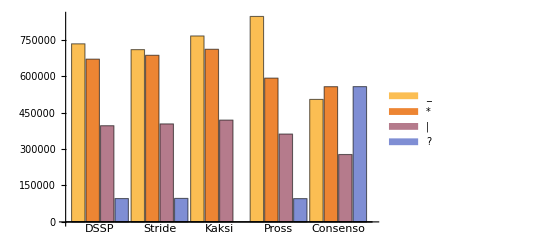

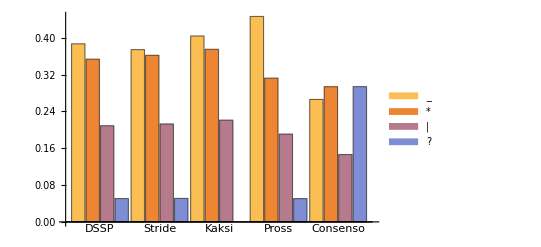

```mathematica
BarChart[{dssp3, stride3, kaksi3, pross3,all3}, ChartLabels->{{"DSSP","Stride","Kaksi","Pross","Consenso"}, None}, ChartLegends->Automatic]
BarChart[{dssp3, stride3, kaksi3, pross3,all3}/Total[Values[all3]], ChartLabels->{{"DSSP","Stride","Kaksi","Pross","Consenso"}, None}, ChartLegends->Automatic]
```

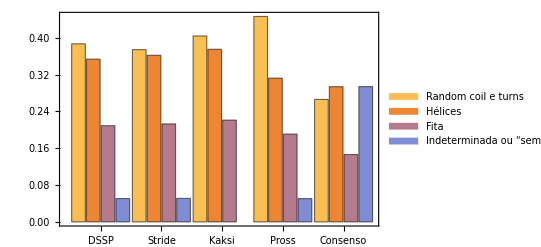

```mathematica
p1 =BarChart[{dssp3, stride3, kaksi3, pross3,all3}/Total[Values[all3]], ChartLabels->{{"DSSP","Stride","Kaksi","Pross","Consenso"}, None}, ChartLegends->{"Random coil e turns", "Hélices", "Fita", "Indeterminada ou \"sem consenso\""}, FrameTicks-> {{ Automatic, {{100000/Total[Values[all3]], 100000}, {200000/Total[Values[all3]], 200000}, {300000/Total[Values[all3]], 300000}, {400000/Total[Values[all3]], 400000}, {500000/Total[Values[all3]], 500000}, {600000/Total[Values[all3]], 600000}, {700000/Total[Values[all3]], 700000}, {800000/Total[Values[all3]],800000}}}, {Automatic, All}}, Frame-> {True, True, False, True}, PlotRange->All]
```

```mathematica
Export["~/Documentos/PhD-Quali/analises/frequencia_SS_top8000-hom70.pdf", p1]
Export["~/Documentos/PhD-Quali/analises/frequencia_SS_top8000-hom70.svg", p1]
Export["~/Documentos/PhD-Quali/analises/frequencia_SS_top8000-hom70.png", p1]
```

~/Documentos/PhD-Quali/analises/frequencia_SS_top8000-hom70.pdf

~/Documentos/PhD-Quali/analises/frequencia_SS_top8000-hom70.svg

~/Documentos/PhD-Quali/analises/frequencia_SS_top8000-hom70.png